```mathematica
Solve[x^6 + 2x^5 + 2x^3 + 3x^2 - 4x - 4 = 0, x]
```

Set::write: Tag Plus in -4 - 4\ x + 3\ x^2 + 2\ x^3 + 2\ x^5 + x^6 is Protected.

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

```mathematica
a z^2 + b z + c /. z-> 2 c/(sqrt(b^2 - 4a c) - b)
```

c+(4 a c^2)/((-b+(b^2-4 a c) sqrt)^2)+(2 b c)/(-b+(b^2-4 a c) sqrt)

```mathematica
a z^2 + b z + c /. z-> 2 c/(sqrt(b^2 - 4a c) - b) // Simplyfy
```

Simplyfy[c+(4 a c^2)/((-b+(b^2-4 a c) sqrt)^2)+(2 b c)/(-b+(b^2-4 a c) sqrt)]

```mathematica
Clear[x,y,z]
```

```mathematica
Solve[(x^7 + x - 1)(x^2 - 4) == 0]
```

{{x→-2},{x→2},{x→Root[-1+#1+#1^7&,1]},{x→Root[-1+#1+#1^7&,2]},{x→Root[-1+#1+#1^7&,3]},{x→Root[-1+#1+#1^7&,4]},{x→Root[-1+#1+#1^7&,5]},{x→Root[-1+#1+#1^7&,6]},{x→Root[-1+#1+#1^7&,7]}}

```mathematica
x/.N[%](*обращение к предыдущему выводу*)
```

{-2.,2.,0.796544,-0.979808-0.516677 ⅈ,-0.979808+0.516677 ⅈ,-0.123762-1.05665 ⅈ,-0.123762+1.05665 ⅈ,0.705298-0.637624 ⅈ,0.705298+0.637624 ⅈ}

```mathematica
Clear
```

Clear

```mathematica
Clear["Global`*"]
```

```mathematica
pts = {x,y}/.Solve[{x^2+y^3-2==0,x^2+y^2/4-2==0},{x,y}]
```

{{-√2,0},{√2,0},{-(√127)/8,1/4},{(√127)/8,1/4}}

```mathematica
Select[pts, # > 0 &](*берет элемент списка и проверяет условие. но здесь список списков, поэтому ответ пустой*)
```

{}

```mathematica
Select[pts, #[[1]] > 0 &]
```

{{√2,0},{(√127)/8,1/4}}

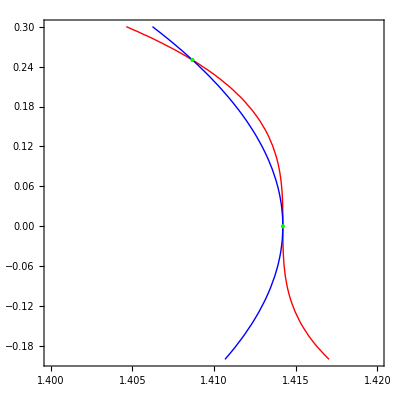

```mathematica
ContourPlot[{x^2+y^3-2==0,x^2+y^2/4-2==0},{x,1.4,1.42},{y,-0.2,0.3},ContourStyle ->{{Red,Thick},{Blue,Thick}},Epilog->{PointSize[Large],Green,Point[Select[pts, #[[1]] > 0 &]]}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
rts = {x,y}/.Solve[{x^2 y + x y^2 = 2, x^3 y + x y^3 = 3},{x,y}]
```

Set::write: Tag Plus in x^2\ y + x\ y^2 is Protected.

Set::write: Tag Plus in x^3\ y + x\ y^3 is Protected.

Solve::naqs: 2 && 3 is not a quantified system of equations and inequalities.

ReplaceAll::reps: {Solve[{2, 3}, {x, y}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x,y}/.Solve[{2,3},{x,y}]

```mathematica
rts = {x,y}/.Solve[{x^2 y + x y^2 == 2, x^3 y + x y^3 == 3},{x,y}]
```

{{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^5)}}

```mathematica
Length[rts]
```

6

```mathematica
yts = {x,y}/.Solve[{x^2 y + x y^2 == 2, x^3 y + x y^3 == 3},{x,y}] //ToReal
```

ToReal[{{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^5)}}]

```mathematica
rts
```

{{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^5)}}

```mathematica
rts = {x,y}/.Solve[{x^2 y + x y^2 == 2, x^3 y + x y^3 == 3},{x,y}, Reals] (*спец домен*)
```

{{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1],9/38+62/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]-24/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^3+35/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^4-18/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^5},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2],9/38+62/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]-24/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^3+35/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^4-18/19 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^5}}

```mathematica
rts = {x,y}/.Solve[{x^2 y + x y^2 == 2, x^3 y + x y^3 == 3},{x,y}] //N
```

{{0.494336,1.77939},{1.77939,0.494336},{-0.99158-0.115464 ⅈ,0.604719+1.38415 ⅈ},{-0.99158+0.115464 ⅈ,0.604719-1.38415 ⅈ},{0.604719-1.38415 ⅈ,-0.99158+0.115464 ⅈ},{0.604719+1.38415 ⅈ,-0.99158-0.115464 ⅈ}}

```mathematica
Element[x/.rts[[6,1]], Reals]
```

ReplaceAll::reps: {0.604719  + 1.38415\ ⅈ}
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(x/.0.604719+1.38415 ⅈ)∈Reals

```mathematica
Select[rts, Element[x /. #, Reals] &]
```

ReplaceAll::reps: {0.494336, 1.77939} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1.77939, 0.494336} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.99158 - 0.115464\ ⅈ, 0.604719  + 1.38415\ ⅈ}
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{}

```mathematica
rts = {x,y}/.Solve[{x^2 y + x y^2 == 2, x^3 y + x y^3 == 3},{x,y}]
```

{{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,3]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,4]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,5]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,6]^5)}}

```mathematica
Select[rts, Element[x /. #, Reals] &]
```

ReplaceAll::reps: {Root[8 - 9\ #1 - 18\ #1^2 + 8\ #1^3 - 6\ #1^5 + 4\ #1^6 &, 1, 0], 1/38\ (« 1 »)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Root[8 - 9\ #1 - 18\ #1^2 + 8\ #1^3 - 6\ #1^5 + 4\ #1^6 &, 2, 0], 1/38\ (« 1 »)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Root[8 - 9\ #1 - 18\ #1^2 + 8\ #1^3 - 6\ #1^5 + 4\ #1^6 &, 3, 0], 1/38\ (« 1 »)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{}

```mathematica
Select[rts, Element[#[[1]], Reals] &]
```

{{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,1]^5)},{Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2],1/38 (9+124 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]-48 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^3+70 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^4-36 Root[8-9 #1-18 #1^2+8 #1^3-6 #1^5+4 #1^6&,2]^5)}}

```mathematica
Clear["Global`*"]
```

```mathematica
(*FindRoots[f_,{x_,a_,b_},opts___] - три подчеркивания - аргумента в функции может и не быть, функция делается с отложенным присваиванием!!!*)
```

```mathematica
FindRoots[f_,{x_,a_,b_},opts___]:=Module[{p,seeds},p=Plot[f,{x,a-(b-a)/100,b+(b-a)/100},Mesh->{{0}},MeshFunctions->(f/.x->#1&),Evaluate[Sequence@@FilterRules[{opts},Options[Graphics]]]];
seeds=Union[Cases[Normal[p],Point[{z_,_}]:>z,Infinity],SameTest -> (Abs[#1-#2]<10^-6&)];
Select[If[seeds=={},{},Union[Table[Re[x]/.FindRoot[f==0,{x,s},Evaluate[Sequence@@FilterRules[{opts},Options[FindRoot]]]],{s,seeds}],(SameTest -> (Abs[#1-#2]<10^-6&))]],a≤#≤b&]]
```

```mathematica
g[x_]:=-Cos[x^3]+Sin[x^2]
```

```mathematica
roots = FindRoots[g[x], {x, 0, pi}]
```

Plot::plln: Limiting value -pi/100 in {x, 0 - pi - 0/100, pi + pi - 0/100} is not a machine-sized real number.

{}

```mathematica
roots = FindRoots[g[x], {x, 0, Pi}]
```

{0.907468,1.70421,2.08451,2.12645,2.43736,2.61184,2.69009,2.90604,2.9652,3.09625}

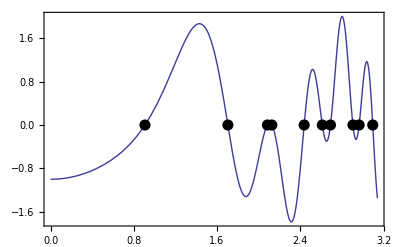

```mathematica
Plot[g[x],{x,0,Pi},Frame->True,AxesStyle->GrayLevel[0.6],Epilog->{PointSize[0.02],Point[{#,0}&/@roots]}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
num = 55
```

55

```mathematica
nsol=NSolve[{2x  y^4 + x^2 y^3 - 2 x^3 y^2 - y^5 - x^4 y + 2y == num},{x,y}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with 151145\ x/110742 - 17791\ y/18457 == 1.

{{x→-11.5648,y→-17.4124},{x→-4.71644+8.53574 ⅈ,y→-7.71558+12.086 ⅈ},{x→-4.71644-8.53574 ⅈ,y→-7.71558-12.086 ⅈ},{x→6.24204+5.32382 ⅈ,y→7.80086+7.53817 ⅈ},{x→6.24204-5.32382 ⅈ,y→7.80086-7.53817 ⅈ}}

```mathematica
{x,y}/.nsol3
```

ReplaceAll::reps: {nsol3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{x,y}/.nsol3

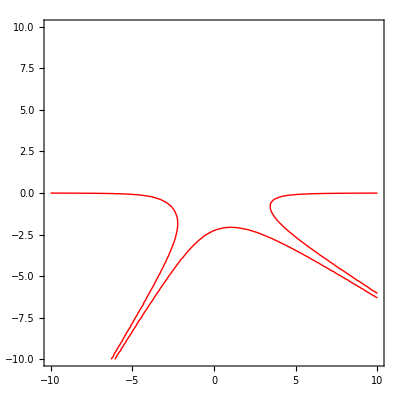

```mathematica
ContourPlot[{2x  y^4 + x^2 y^3 - 2 x^3 y^2 - y^5 - x^4 y + 2y == num},{x,-10,10},{y,-10,10},ContourStyle ->{{Red,Thick},{Blue,Thick}}]
```

```mathematica
Plot3D[{2x  y^4 + x^2 y^3 - 2 x^3 y^2 - y^5 - x^4 y + 2y == num},{x,0, 10},{y,0,10}]
```

-Graphics3D-